```mathematica
Needs["dsvsolve`"];
```

## Input ATTENZIONE: DSV SOLVE ADOPERA UN SISTEMA DI RIFERIMENTO NEL QUALE L’ASSE X E` ENTRANTE NEL PIANO. QUINDI v(z) e` lo spostamento verso l’alto e Q(z) che rappresenta il taglio, ha la covenzione opposta rispetto a quella del libro

Edit or simply evaluate the following cell to see the input

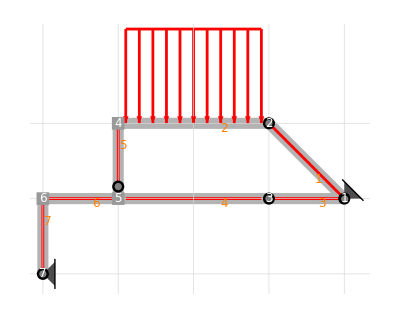

```mathematica
example={$$nodes->{{2*L, 0}, {L, L}, {L, 0}, {-L, L}, {-L, 0}, {-2*L, 0}, {-2*L, -L}},
$$edges->{{1, 2}, {2, 4}, {1, 3}, {3, 5}, {4, 5}, {5, 6}, {6, 7}},$$absname->s,
$$constraints->{{{"hinge", 1, 3},{"hinge",1}}, {{"hinge", 1, 2}}, {{"hinge", 3, 4}}, {{"clamp", 2, 5}}, {{"hinge", 5, 6}, {"clamp", 4, 6}}, {{"clamp", 6, 7}}, {{"hinge", 7}}},
$$bodyloads->{{2, {0, q, 0}}},
$$nodalloads->{{1, {0, 0, 0}}},
$$predeformations->{{1, {0, 0, 0}}},
$$cdisplacements->{{1, {0, 0, 0}}},
$$EIoverEAL2->0};
(*All constraints are initialized to hinge constraints; use "BFConstraintsPalette[BFConstraintTypes];" to input different constraints.*)
BFShowInput[example]
```

## Output

Evaluate the following cell to solve the problem and see the output

```mathematica
BFClassify[example]; sol = {{Ns, Qs, Ms}, details} = BFForcesSolve[example];
(*A=Transpose[First[BFStaticProblem[example]]];MatrixForm[A]
BFShowRigidMotions[example]*)
(*BFEquations[example,"Nodal"]; sol = {{us, vs}, {Ns, Qs, Ms}, details} = BFDisplacementsSolve[example];*)
gsol=BFShowOutput[example, sol]
```

BFClassify::sd: Statically determined system.

BFClassify::kd: Kinematically determined system.

123

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Dimensionless abscissa

s

Static equilibrium matrix

{{-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,√2 L,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,2 L,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,L,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,2 L,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,L,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,L,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,L,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,√2,√2,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-√2,√2,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-1,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0}}

Static equilibrium vector

{0,0,0,0,-2 L q,-2 L^2 q,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Fredholm condition: are the loads orthogonal to allowed rigid motions?

True

Bending stiffnesses

{EI,EI,EI,EI,EI,EI,EI}

Axial stiffnesses

{∞,∞,∞,∞,∞,∞,∞}

Degree of static undetermination

1

Some possible choices for the static unknowns

{{("N")_("3")[0]},{("N")_("3")[1]},{("N")_("4")[0]},{("N")_("4")[1]},{("N")_("6")[0]},{("N")_("6")[1]},{("Q")_("7")[0]},{("Q")_("7")[1]},{("M")_("7")[1]}}

Actually chosen static unknowns

{("N")_("3")[0]}

Reactions in the auxiliary problem 0

{{-2/3 √2 L q,0,0,-2/3 √2 L q,0,0},{-(2 L q)/3,(2 L q)/3,0,-(2 L q)/3,-(4 L q)/3,(2 L^2 q)/3},{0,0,0,0,0,0},{0,0,0,0,0,0},{-(4 L q)/3,(2 L q)/3,(2 L^2 q)/3,-(4 L q)/3,(2 L q)/3,0},{-(2 L q)/3,-(4 L q)/3,0,-(2 L q)/3,-(4 L q)/3,(4 L^2 q)/3},{-(4 L q)/3,(2 L q)/3,(4 L^2 q)/3,-(4 L q)/3,(2 L q)/3,(2 L^2 q)/3}}

Reactions in the auxiliary problem 1

{{0,0,0,0,0,0},{0,0,0,0,0,0},{1,0,0,1,0,0},{1,0,0,1,0,0},{0,0,0,0,0,0},{1,0,0,1,0,0},{0,-1,0,0,-1,L}}

Internal actions (N,Q,M) in the auxiliary problem 0

{{-2/3 √2 L q,-(2 L q)/3,0,0,-(4 L q)/3,-(2 L q)/3,-(4 L q)/3},{0,2/3 L q (1-3 s),0,0,(2 L q)/3,-(4 L q)/3,(2 L q)/3},{0,2/3 L^2 q s (-2+3 s),0,0,-2/3 L^2 q (-1+s),4/3 L^2 q s,-2/3 L^2 q (-2+s)}}

Internal actions (N,Q,M) in the auxiliary problem 1

{{0,0,1,1,0,1,0},{0,0,0,0,0,0,-1},{0,0,0,0,0,0,L s}}

Mohr's Integrals: coefficient matrix ηij

{{L^3/(3 EI)}}

Mohr's Integrals: vector ηi0

{(4 L^4 q)/(9 EI)}

Mohr's Integrals: solution for the static unknowns

{("N")_("3")[0]→-(4 L q)/3}

Actual reactions

{{-2/3 √2 L q,0,0,-2/3 √2 L q,0,0},{-(2 L q)/3,(2 L q)/3,0,-(2 L q)/3,-(4 L q)/3,(2 L^2 q)/3},{-(4 L q)/3,0,0,-(4 L q)/3,0,0},{-(4 L q)/3,0,0,-(4 L q)/3,0,0},{-(4 L q)/3,(2 L q)/3,(2 L^2 q)/3,-(4 L q)/3,(2 L q)/3,0},{-2 L q,-(4 L q)/3,0,-2 L q,-(4 L q)/3,(4 L^2 q)/3},{-(4 L q)/3,2 L q,(4 L^2 q)/3,-(4 L q)/3,2 L q,-(2 L^2 q)/3}}

Actual internal actions (N,Q,M)

{{-2/3 √2 L q,-(2 L q)/3,-(4 L q)/3,-(4 L q)/3,-(4 L q)/3,-2 L q,-(4 L q)/3},{0,2/3 L q (1-3 s),0,0,(2 L q)/3,-(4 L q)/3,2 L q},{0,2/3 L^2 q s (-2+3 s),0,0,-2/3 L^2 q (-1+s),4/3 L^2 q s,2/3 L^2 q (2-3 s)}}

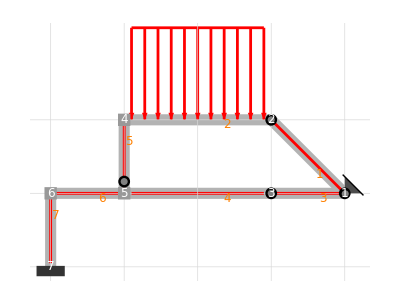

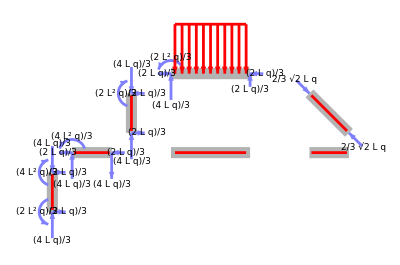

-Graphics-

-Graphics-

-Graphics-

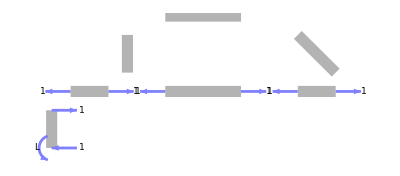

-Graphics-

-Graphics-

-Graphics-

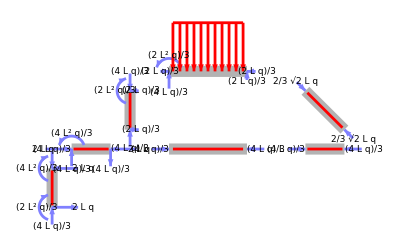

-Graphics-

-Graphics-

-Graphics-

```mathematica
BFEquations[example,"Nodal"]
```

Natural constraints in node 1: M_3[0]==0
M_1[0]==0

Natural constraints in node 2: √2 N_1[1]-2 N_2[0]+√2 Q_1[1]==0
-√2 N_1[1]+√2 Q_1[1]-2 Q_2[0]==0
M_2[0]==0
-M_1[1]==0

Natural constraints in node 3: N_3[1]-N_4[0]==0
Q_3[1]-Q_4[0]==0
M_4[0]==0
-M_3[1]==0

Natural constraints in node 4: N_2[1]+Q_5[0]==0
-N_5[0]+Q_2[1]==0
-M_2[1]+M_5[0]==0

Natural constraints in node 5: N_4[1]-N_6[0]-Q_5[1]==0
N_5[1]+Q_4[1]-Q_6[0]==0
-M_4[1]+M_6[0]==0
-M_5[1]==0

Natural constraints in node 6: N_6[1]+Q_7[0]==0
-N_7[0]+Q_6[1]==0
-M_6[1]+M_7[0]==0

Natural constraints in node 7: {}

Kinematical constraints in node 1: u_1[0]==0
u_3[0]==0
v_1[0]==0
v_3[0]==0

Kinematical constraints in node 2: -u_1[1]+v_1[1]-√2 v_2[0]==0
-√2 u_1[1]+u_2[0]-v_2[0]==0

Kinematical constraints in node 3: u_3[1]-u_4[0]==0
v_3[1]-v_4[0]==0

Kinematical constraints in node 4: u_5[0]-v_2[1]==0
u_2[1]+v_5[0]==0
v_2'[1]-v_5'[0]==0

Kinematical constraints in node 5: u_4[1]+v_5[1]==0
u_6[0]+v_5[1]==0
u_5[1]-v_4[1]==0
-v_4[1]+v_6[0]==0
v_4'[1]-v_6'[0]==0

Kinematical constraints in node 6: u_7[0]-v_6[1]==0
u_6[1]+v_7[0]==0
v_6'[1]-v_7'[0]==0

Kinematical constraints in node 7: u_7[1]==0
v_7[1]==0
v_7'[1]==0

```mathematica
BFShowEquilibrium[example,reazioni1,ImageSize->400]
```

BFShowEquilibrium[{$$nodes→{{2 L,0},{L,L},{L,0},{-L,L},{-L,0},{-2 L,0},{-2 L,-L}},$$edges→{{1,2},{2,4},{1,3},{3,5},{4,5},{5,6},{6,7}},$$absname→s,$$constraints→{{{hinge,1,3},{hinge,1}},{{hinge,1,2}},{{hinge,3,4}},{{clamp,2,5}},{{hinge,5,6},{clamp,4,6}},{{clamp,6,7}},{{clamp,7}}},$$bodyloads→{{2,{0,q,0}}},$$nodalloads→{{1,{0,0,0}}},$$predeformations→{{1,{0,0,0}}},$$cdisplacements→{{1,{0,0,0}}},$$EIoverEAL2→0},reazioni1,ImageSize→400]

```mathematica
{B,f}=BFStaticProblem[example];
reactions=Simplify[LinearSolve[B,f]];
{N1,Q1,M1}=BFReactionsToStresses[example][reactions];
```

{-2/3 √2 L q,0,0,-2/3 √2 L q,0,0,-(2 L q)/3,(2 L q)/3,0,-(2 L q)/3,-(4 L q)/3,(2 L^2 q)/3,-(2 L q)/3,0,0,-(2 L q)/3,0,0,-(2 L q)/3,0,0,-(2 L q)/3,0,0,-(4 L q)/3,(2 L q)/3,(2 L^2 q)/3,-(4 L q)/3,(2 L q)/3,0,-(4 L q)/3,-(4 L q)/3,0,-(4 L q)/3,-(4 L q)/3,(4 L^2 q)/3,-(4 L q)/3,(4 L q)/3,(4 L^2 q)/3,-(4 L q)/3,(4 L q)/3,0}

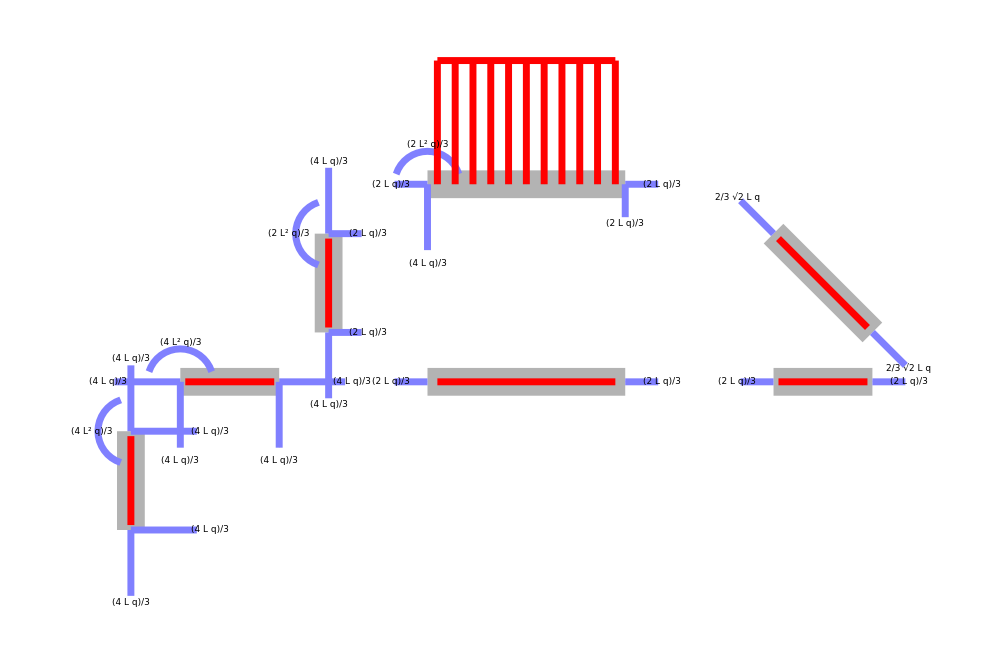

```mathematica
BFShowEquilibrium[example,reactions,ImageSize->1000]
```